```mathematica
mu = 1.25
```

1.25

```mathematica
sigma = 0.2
```

0.2

```mathematica
nordist := NormalDistribution[mu, sigma];
```

```mathematica
distFn=PDF[NormalDistribution[mu,sigma],x];
```

```mathematica
1.9947114020071635 ⅇ^(-12.5 (-1.25+x)^2)
```

1.99471 ⅇ^(-12.5 (-1.25+x)^2)

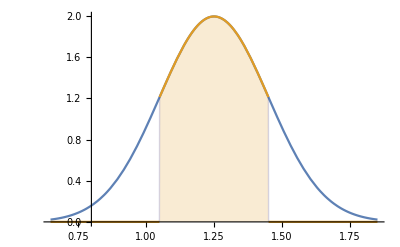

```mathematica
Plot[Evaluate[distFn*{1,Boole[mu-sigma<x<mu+sigma]}],{x,mu-3 sigma,mu+3 sigma},Filling->{2->Axis}]
```

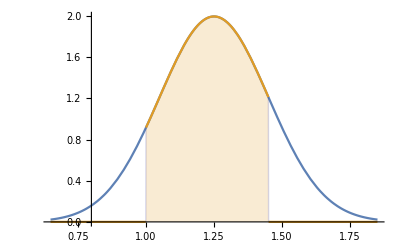

```mathematica
Plot[Evaluate[distFn*{1,Boole[1.0<x<mu+sigma]}],{x,mu-3 sigma,mu+3 sigma},Filling->{2->Axis}]
```

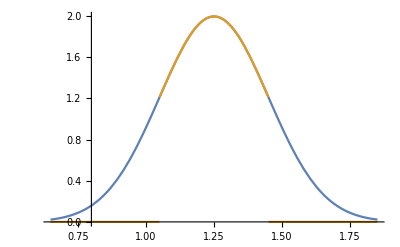

```mathematica
Plot[Evaluate[distFn*{1,Boole[mu-sigma<x<mu+sigma]}],{x,mu-3 sigma,mu+3 sigma}]
```

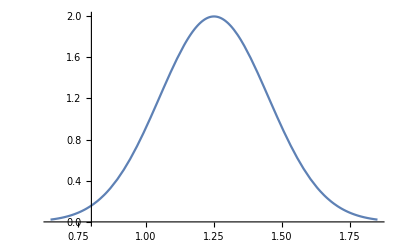

```mathematica
Plot[Evaluate[distFn],{x,mu-3 sigma,mu+3 sigma}]
```

```mathematica
1 - CDF[nordist,1.5]
```

0.10565

```mathematica
1-CDF[nordist,1.5]
```

0.10565

```mathematica
1-CDF[nordist,1.5]
```

0.10565

```mathematica
(1.5 - 1.25)/0.2
```

1.25

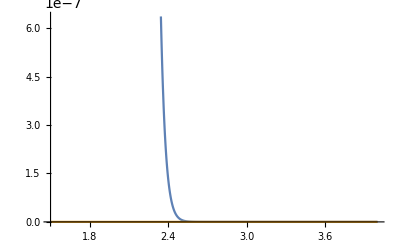

```mathematica
Plot[Evaluate[distFn*{1,Boole[mu-sigma<x<mu+sigma]}],{x,1.5,4},Filling->{2->Axis}]
```

```mathematica
Plot[Evaluate[distFn*{1,Boole[mu-sigma<x<mu+sigma]}],{x,mu-3 sigma,mu+3 sigma},Filling->{2->Axis}]
```

-Graphics-

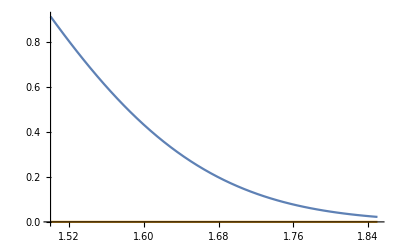

```mathematica
Plot[Evaluate[distFn*{1,Boole[mu-sigma<x<mu+sigma]}],{x,1.5,mu+3 sigma},Filling->{2->Axis}]
```

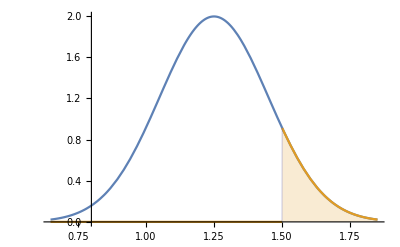

```mathematica
Plot[Evaluate[distFn*{1,Boole[1.5<x]}],{x,mu-3 sigma,mu+3 sigma},Filling->{2->Axis}]
```

```mathematica
(0.9*0.2) - 1.25
```

-1.07

```mathematica
(0.9*0.2) + 1.25
```

1.43

```mathematica
(1.29*0.2) + 1.25
```

1.508

```mathematica
CDF[nordist,1]
```

0.10565

```mathematica
CDF[nordist,0.75]
```

0.00620967

```mathematica
0.10564977366685531 - 0.006209665325776143
```

0.0994401

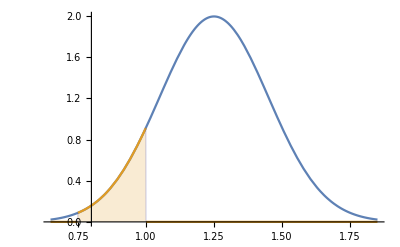

```mathematica
Plot[Evaluate[distFn*{1,Boole[0.75<x < 1]}],{x,mu-3 sigma,mu+3 sigma},Filling->{2->Axis}]
```